```mathematica
Centry[m_,k_]:=1/(m+k+1)
```

```mathematica
limit=20;
Cmat=Table[Centry[m,k],{m,0,limit},{k,0,limit}];
Imat = Inverse[Cmat];
Imat // MatrixForm
```

(441 | -97020 | 7066290 | -254386440 | 5405711850 | -74959204320 | 722820898800 | -5059746291600 | 26493393776850 | -105973575107400 | 328518082832940 | -796407473534400 | 1516237305382800 | -2266024983868800 | 2643695814513600 | -2379326233062240 | 1618291739398950 | -803857334603400 | 275003824995900 | -57895542104400 | 5651707681620
-97020 | 28459200 | -2331875700 | 89544026880 | -1982094345000 | 28270328486400 | -278286046038000 | 1978922994048000 | -10491383935632600 | 42389430042960000 | -132502293409285800 | 323463958481664000 | -619491241913544000 | 930580926708787200 | -1090524523486860000 | 985320981221068800 | -672490122816897000 | 335081583687312000 | -114951598848286200 | 24260989072320000 | -2373717226280400
7066290 | -2331875700 | 203805936180 | -8152237447200 | 185608977592500 | -2702466713746800 | 27024667137468000 | -194577603389769600 | 1041985177243510500 | -4245124796177265000 | 13362346666121052600 | -32814263359541664000 | 63167456967117703200 | -95311843352751564000 | 112131580415001840000 | -101665966242935001600 | 69602727711548839500 | -34777279866946894200 | 11960440165881207000 | -2530035189962280000 | 248053450146301800
-254386440 | 89544026880 | -8152237447200 | 335406340684800 | -7795577058885000 | 115305246453196800 | -1167465620338617600 | 8490659057008128000 | -45847347798714462000 | 188091683276777280000 | -595578879975681201600 | 1470078998507466547200 | -2842535563520296644000 | 4305852687936070656000 | -5083298312146750080000 | 4623126043889254809600 | -3173884383646627081200 | 1589818508203286592000 | -548005622145829848000 | 116161615678268160000 | -11410458706729882800
5405711850 | -1982094345000 | 185608977592500 | -7795577058885000 | 184062236112562500 | -2756516048021736000 | 28191641400222300000 | -206738703601630200000 | 1124141700833864212500 | -4639314955822296750000 | 14765393066063763123000 | -36608412560488668900000 | 71063389088007416100000 | -108020089133118439200000 | 127918526605008678000000 | -116661696263767914336000 | 80291718038679554137500 | -40310028936688445550000 | 13923512410498665975000 | -2956978628268414750000 | 290966697021612011400
-74959204320 | 28270328486400 | -2702466713746800 | 115305246453196800 | -2756516048021736000 | 41698570035528806400 | -430016503491390816000 | 3175506487321039872000 | -17369595194598679032000 | 72051654140557483392000 | -230340131830594704718800 | 573330809417911953408000 | -1116800639178640992576000 | 1702851426165875521536000 | -2022136068571977181824000 | 1848810119837236280524800 | -1275324452338008336264000 | 641595451875778528128000 | -222033611239418726748000 | 47235959399410964582400 | -4655467152345792182400
722820898800 | -278286046038000 | 27024667137468000 | -1167465620338617600 | 28191641400222300000 | -430016503491390816000 | 4465555997795212320000 | -33172701697907291520000 | 182380749543286129836000 | -759919789763692207650000 | 2438895513500414520552000 | -6091639850065314504960000 | 11902743654403936894560000 | -18199224617147794636416000 | 21665743591842612662400000 | -19853699582343048694272000 | 13723600084941611444580000 | -6917200965535737256380000 | 2397963001385722248878400 | -510965906964782068800000 | 50434227483746081976000
-5059746291600 | 1978922994048000 | -194577603389769600 | 8490659057008128000 | -206738703601630200000 | 3175506487321039872000 | -33172701697907291520000 | 247689506011041110016000 | -1367855621574645973770000 | 5721749005279564857600000 | -18427210546447576377504000 | 46168217811021330984960000 | -90460851773469920398656000 | 138660758987792721039360000 | -165447496519525405785600000 | 151923962021407676964864000 | -105214267317885687741780000 | 53124103415314462128998400 | -18445869241428632683680000 | 3936329949950913715200000 | -389064040588898346672000
26493393776850 | -10491383935632600 | 1041985177243510500 | -45847347798714462000 | 1124141700833864212500 | -17369595194598679032000 | 182380749543286129836000 | -1367855621574645973770000 | 7583552490200610766342500 | -31832195637879106920450000 | 102834745697527346461959000 | -258361675140895151441616000 | 507496147598186904617460000 | -779671327348263474764640000 | 932215717481619372001200000 | -857638460083089822241104000 | 594986681682643564179765900 | -300898242000804570652530000 | 104633339296576074979995000 | -22359320625307115349900000 | 2212801730849359346697000
-105973575107400 | 42389430042960000 | -4245124796177265000 | 188091683276777280000 | -4639314955822296750000 | 72051654140557483392000 | -759919789763692207650000 | 5721749005279564857600000 | -31832195637879106920450000 | 134030297422648871244000000 | -434191148500671018394938000 | 1093594392130773127795200000 | -2153013959507459595346800000 | 3314544773267979989337600000 | -3970548426310601028894000000 | 3659257429687849908228710400 | -2542678126848904120426350000 | 1287794945188628615138400000 | -448428596985326035628550000 | 95948042530053521808000000 | -9506851880686136452476000
328518082832940 | -132502293409285800 | 13362346666121052600 | -595578879975681201600 | 14765393066063763123000 | -230340131830594704718800 | 2438895513500414520552000 | -18427210546447576377504000 | 102834745697527346461959000 | -434191148500671018394938000 | 1410087444178369688311179600 | -3559649746385666530973376000 | 7022569880097809514909432000 | -10831656106975319606822832000 | 12997987328370383528187398400 | -11998142149264969410634521600 | 8349401582460142196925933000 | -4234545735839894164135446000 | 1476412497936514823510826000 | -316276730859899759053104000 | 31372611206264250293170800
-796407473534400 | 323463958481664000 | -32814263359541664000 | 1470078998507466547200 | -36608412560488668900000 | 573330809417911953408000 | -6091639850065314504960000 | 46168217811021330984960000 | -258361675140895151441616000 | 1093594392130773127795200000 | -3559649746385666530973376000 | 9004647579789828378746880000 | -17798248731928332654866880000 | 27499874017048084158809702400 | -33052733193567408844723200000 | 30555415574497871287566336000 | -21292452677820433465596240000 | 10812633169884711231306240000 | -3774409912080126050187456000 | 809452576980815165798400000 | -80376111354891880916388000
1516237305382800 | -619491241913544000 | 63167456967117703200 | -2842535563520296644000 | 71063389088007416100000 | -1116800639178640992576000 | 11902743654403936894560000 | -90460851773469920398656000 | 507496147598186904617460000 | -2153013959507459595346800000 | 7022569880097809514909432000 | -17798248731928332654866880000 | 35240532489218098656636422400 | -54537009769386224593793280000 | 65646400648335270344380800000 | -60769810885887507404512512000 | 42401349729107932159937340000 | -21557687382457643017416816000 | 7533600429353477398559640000 | -1617324191897214676976100000 | 160752222709783761832776000
-2266024983868800 | 930580926708787200 | -95311843352751564000 | 4305852687936070656000 | -108020089133118439200000 | 1702851426165875521536000 | -18199224617147794636416000 | 138660758987792721039360000 | -779671327348263474764640000 | 3314544773267979989337600000 | -10831656106975319606822832000 | 27499874017048084158809702400 | -54537009769386224593793280000 | 84524596337738194242232320000 | -101882325942809430559833600000 | 94434376598024741153390592000 | -65968806047969106287492256000 | 33577157671474397217431040000 | -11746175817364741387695060000 | 2524150935318873327667200000 | -251115898197532030318656000
2643695814513600 | -1090524523486860000 | 112131580415001840000 | -5083298312146750080000 | 127918526605008678000000 | -2022136068571977181824000 | 21665743591842612662400000 | -165447496519525405785600000 | 932215717481619372001200000 | -3970548426310601028894000000 | 12997987328370383528187398400 | -33052733193567408844723200000 | 65646400648335270344380800000 | -101882325942809430559833600000 | 122961427862011381710144000000 | -114108205055946562227013632000 | 79800975058027144702611600000 | -40659839367801027880482900000 | 14237788869533019863872800000 | -3062389002408927199008000000 | 304926447811288893958368000
-2379326233062240 | 985320981221068800 | -101665966242935001600 | 4623126043889254809600 | -116661696263767914336000 | 1848810119837236280524800 | -19853699582343048694272000 | 151923962021407676964864000 | -857638460083089822241104000 | 3659257429687849908228710400 | -11998142149264969410634521600 | 30555415574497871287566336000 | -60769810885887507404512512000 | 94434376598024741153390592000 | -114108205055946562227013632000 | 106010203406814870714128793600 | -74214906803965244573428788000 | 37850614102389320499649536000 | -13266269158435472626102656000 | 2855896486817925250732032000 | -284598017957202967694476800
1618291739398950 | -672490122816897000 | 69602727711548839500 | -3173884383646627081200 | 80291718038679554137500 | -1275324452338008336264000 | 13723600084941611444580000 | -105214267317885687741780000 | 594986681682643564179765900 | -2542678126848904120426350000 | 8349401582460142196925933000 | -21292452677820433465596240000 | 42401349729107932159937340000 | -65968806047969106287492256000 | 79800975058027144702611600000 | -74214906803965244573428788000 | 52006658177021099416986082500 | -26548483351917141733727070000 | 9313039398053473528815369000 | -2006502794286682508516700000 | 200107981376158336660179000
-803857334603400 | 335081583687312000 | -34777279866946894200 | 1589818508203286592000 | -40310028936688445550000 | 641595451875778528128000 | -6917200965535737256380000 | 53124103415314462128998400 | -300898242000804570652530000 | 1287794945188628615138400000 | -4234545735839894164135446000 | 10812633169884711231306240000 | -21557687382457643017416816000 | 33577157671474397217431040000 | -40659839367801027880482900000 | 37850614102389320499649536000 | -26548483351917141733727070000 | 13564267124340858969837024000 | -4762146251215347863638770000 | 1026801018454757943196800000 | -102477443749728144725628000
275003824995900 | -114951598848286200 | 11960440165881207000 | -548005622145829848000 | 13923512410498665975000 | -222033611239418726748000 | 2397963001385722248878400 | -18445869241428632683680000 | 104633339296576074979995000 | -448428596985326035628550000 | 1476412497936514823510826000 | -3774409912080126050187456000 | 7533600429353477398559640000 | -11746175817364741387695060000 | 14237788869533019863872800000 | -13266269158435472626102656000 | 9313039398053473528815369000 | -4762146251215347863638770000 | 1673186520697284384521730000 | -361031644646738721255600000 | 36056878356385828699758000
-57895542104400 | 24260989072320000 | -2530035189962280000 | 116161615678268160000 | -2956978628268414750000 | 47235959399410964582400 | -510965906964782068800000 | 3936329949950913715200000 | -22359320625307115349900000 | 95948042530053521808000000 | -316276730859899759053104000 | 809452576980815165798400000 | -1617324191897214676976100000 | 2524150935318873327667200000 | -3062389002408927199008000000 | 2855896486817925250732032000 | -2006502794286682508516700000 | 1026801018454757943196800000 | -361031644646738721255600000 | 77955550800915243456000000 | -7790682858166467142884000
5651707681620 | -2373717226280400 | 248053450146301800 | -11410458706729882800 | 290966697021612011400 | -4655467152345792182400 | 50434227483746081976000 | -389064040588898346672000 | 2212801730849359346697000 | -9506851880686136452476000 | 31372611206264250293170800 | -80376111354891880916388000 | 160752222709783761832776000 | -251115898197532030318656000 | 304926447811288893958368000 | -284598017957202967694476800 | 200107981376158336660179000 | -102477443749728144725628000 | 36056878356385828699758000 | -7790682858166467142884000 | 779068285816646714288400)

```mathematica
ffunc[n_,x_]:=Sum[Imat[[k+1,n+1]]x^k, {k,0,limit}]
```

```mathematica
Integrate[x^4 ffunc[2,x],{x,0,1}]
Grid[Table[Integrate[x^n ffunc[m,x],{x,0,1}],{n,0,limit},{m,0,limit}]]
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1

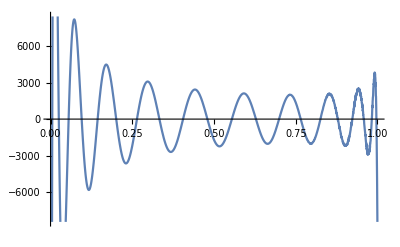

```mathematica
Plot[ffunc[1,x],{x,0,1}]
```

```mathematica
unnormal[l_,m_]:=(-1)^m LegendreP[l,m,Cos[θ]]Exp[I m ϕ]
```

```mathematica
θ=1.21;
ϕ=4.241;
```

```mathematica
-1/3(unnormal[2,0]-1)+2 unnormal[2,-2]+1/12 unnormal[2,2]
(Sin[θ]Cos[ϕ])^2
```

0.180528-5.55112×10^-17 ⅈ

0.180528

```mathematica
-1/3(unnormal[2,0]-1)-2 unnormal[2,-2]-1/12 unnormal[2,2]
(Sin[θ]Sin[ϕ])^2
```

0.694849+5.55112×10^-17 ⅈ

0.694849

```mathematica
2/3 unnormal[2,0]+1/3
(Cos[θ])^2
```

0.124623

0.124623

```mathematica
unnormal[2,1]/6-unnormal[2,-1]
Sin[θ]Cos[θ]Cos[ϕ]
```

-0.149993+0. ⅈ

-0.149993

```mathematica
unnormal[2,1]/(6 I)+unnormal[2,-1]/I
Sin[θ]Cos[θ]Sin[ϕ]
```

-0.294269+0. ⅈ

-0.294269

```mathematica
unnormal[2,2]/(12I)-(2 unnormal[2,-2])/I
Sin[θ]^2Sin[ϕ]Cos[ϕ]
```

0.354175-2.77556×10^-17 ⅈ

0.354175